# Plots Across Dataset for Specific Run

## Data Selection

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
plotsDir= "kl_div_plots";
dataDir = "mlflow_data";
bcRateKHz = 28608.8064;
```

```mathematica
(*Set the name of the experiment.*)
experiments =FileNameTake/@(FileNames[All, dataDir]);
experimentName =.;
PopupMenu[Dynamic[experimentName],experiments]
```

```mathematica
(*Get the experiment directory and the names of all the runs in that directory.*)
experimentDir=FileNameJoin[{dataDir, experimentName}];
runDirs = FileNames[All, experimentDir];
runNames = FileNameTake/@runDirs;

(*Select which run to plot.*)
desiredRun=runNames[[1]];
PopupMenu[Dynamic[desiredRun, (desiredRun=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"datasetSelection", "labels", "importData", "plotGrid"}}])&
],runNames]
```

```mathematica
(*Select which metric to plot.*)
availableMetrics = {"kl", "reco", "loss","rate_0.3", "rate_1", "z_mean_squared_rate0.3", "loss_reco_full_rate0.3","loss_total_full_rate0.3", "loss_kl_full_rate0.3"};
desiredMetric=availableMetrics[[1]];
PopupMenu[Dynamic[desiredMetric, (desiredMetric=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"datasetSelection", "labels", "importData", "plotGrid"}}])&
],availableMetrics]
desiredMetricPlotStyling = <|"kl"->"α × D_KL(μ, σ)", "reco"->"(1-α)×(𝒳 - 𝒳̂)^2", "loss"->"α × D_KL[𝒵 || 𝒩(0, 1)] + (1-α)×(𝒳 - 𝒳̂)^2", "z_mean_squared_rate0.3"->"TPR @ 10^-5 FPR (μ^2)", "loss_reco_full_rate0.3"->"TPR @ 10^-5 FPR (MSE)", "loss_total_full_rate0.3"->"TPR @ 10^-5 FPR (total)", "loss_kl_full_rate0.3"->"TPR @ 10^-5 FPR (KL)"|>;
```

```mathematica
desiredRunDir = Select[runDirs, StringContainsQ[desiredRun]];
datasetPaths = FileNames[All, desiredRunDir];
datasetPaths = Select[datasetPaths, StringContainsQ[desiredMetric <> "." ]];
datasetPaths = Select[datasetPaths, StringFreeQ["test"]];
datasetPaths =If[StringContainsQ[desiredMetric, "rate"],DeleteCases[datasetPaths,_?(StringContainsQ[#,"main_"]&)], datasetPaths];
```

## Metadata

```mathematica
(*Extract parameters from run names. Will be used as labels for the plots.*)
processDatasetNames[datasetName_] := StringReplace[FileBaseName@StringSplit[datasetName, "/"][[-1]], RegularExpression["^(val_)?|(_loss.*|_rate.*|_cap.*)"]-> ""]
wrapLabel[label_,n_]:=StringJoin@Riffle[Partition[Characters[label],n,n,{1,1},""],"\n"]
datasetNames =processDatasetNames/@datasetPaths;
datasetNamesWrapped = wrapLabel[#, 37] & /@ datasetNames;
Style["List of the datasets that will be plotted: ", "Subsection"]
Framed[Pane[Column[datasetNames], {Automatic, 150}, Scrollbars->True]]
```

List of the datasets that will be plotted:

train
ggXToJpsiJpsiTo2Mu2E_m7_pseudoscalar
ggXToYYTo2Mu2E_m14_pseudoscalar
ggXToYYTo2Mu2E_m18_pseudoscalar
ggXToYYTo2Mu2E_m26_pseudoscalar
GluGluHToBB_M-125
GluGluHToGG_M-125
GluGluHToGG_M-90
GluGluHToTauTau_M-125
GluGlutoHHto2B2WtoLNu2Q_kl-1p00_kt-1p00_c2-0p00
haa-4b-ma15
HHHto4B2Tau_c3-0_d4-0
HHHTo6B_c3_0_d4_0
HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-100000mm
HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-10000mm
HTo2LongLivedTo4b_MH-125_MFF-12_CTau-900mm
HTo2LongLivedTo4b_MH-125_MFF-25_CTau-1500mm
HTo2LongLivedTo4b_MH-125_MFF-50_CTau-3000mm
main_val
SingleNeutrino_E-10-gun
SingleNeutrino_Pt-2To20-gun
SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT-60
SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT60
SUSYGluGluToBBHToBB_NarrowWidth_M-1200_1
SUSYGluGluToBBHToBB_NarrowWidth_M-1200_2
SUSYGluGluToBBHToBB_NarrowWidth_M-120_1
SUSYGluGluToBBHToBB_NarrowWidth_M-120_2
SUSYGluGluToBBHToBB_NarrowWidth_M-350_1
SUSYGluGluToBBHToBB_NarrowWidth_M-350_2
SUSYGluGluToBBHToBB_NarrowWidth_M-600_1
SUSYGluGluToBBHToBB_NarrowWidth_M-600_2
ttHto2B_M-125
ttHto2C_M-125
VBFHto2B_M-125
VBFHToCC_M-125
VBFHToInvisible_M-125
VBFHToTauTau_M125
Wlnu
WToTauTo3Mu
WToTauToMuMuMu

## Import Data

```mathematica
(*Get the data to plot from all the runs inside the experiment.*)
plotData = AssociationThread[datasetNames,BinaryReadList[#, "Real32"] & /@ datasetPaths];
plotData // Dimensions
(*Restrict values to be between 0 and 1, for better plotting visibility if the data is kl divergence related.*)
If[desiredMetric == "kl",plotData =Map[Clip[#,{0,2}]&, plotData]];
If[desiredMetric == "loss",plotData =Map[Clip[#,{0,4}]&, plotData]];
If[StringContainsQ[desiredMetric, "rate"], plotData = plotData/bcRateKHz];
```

{40}

```mathematica
Style["Plotting data for " <> desiredRun, "Title"]
```

Plotting data for scan_lr0.001_alpha0.6

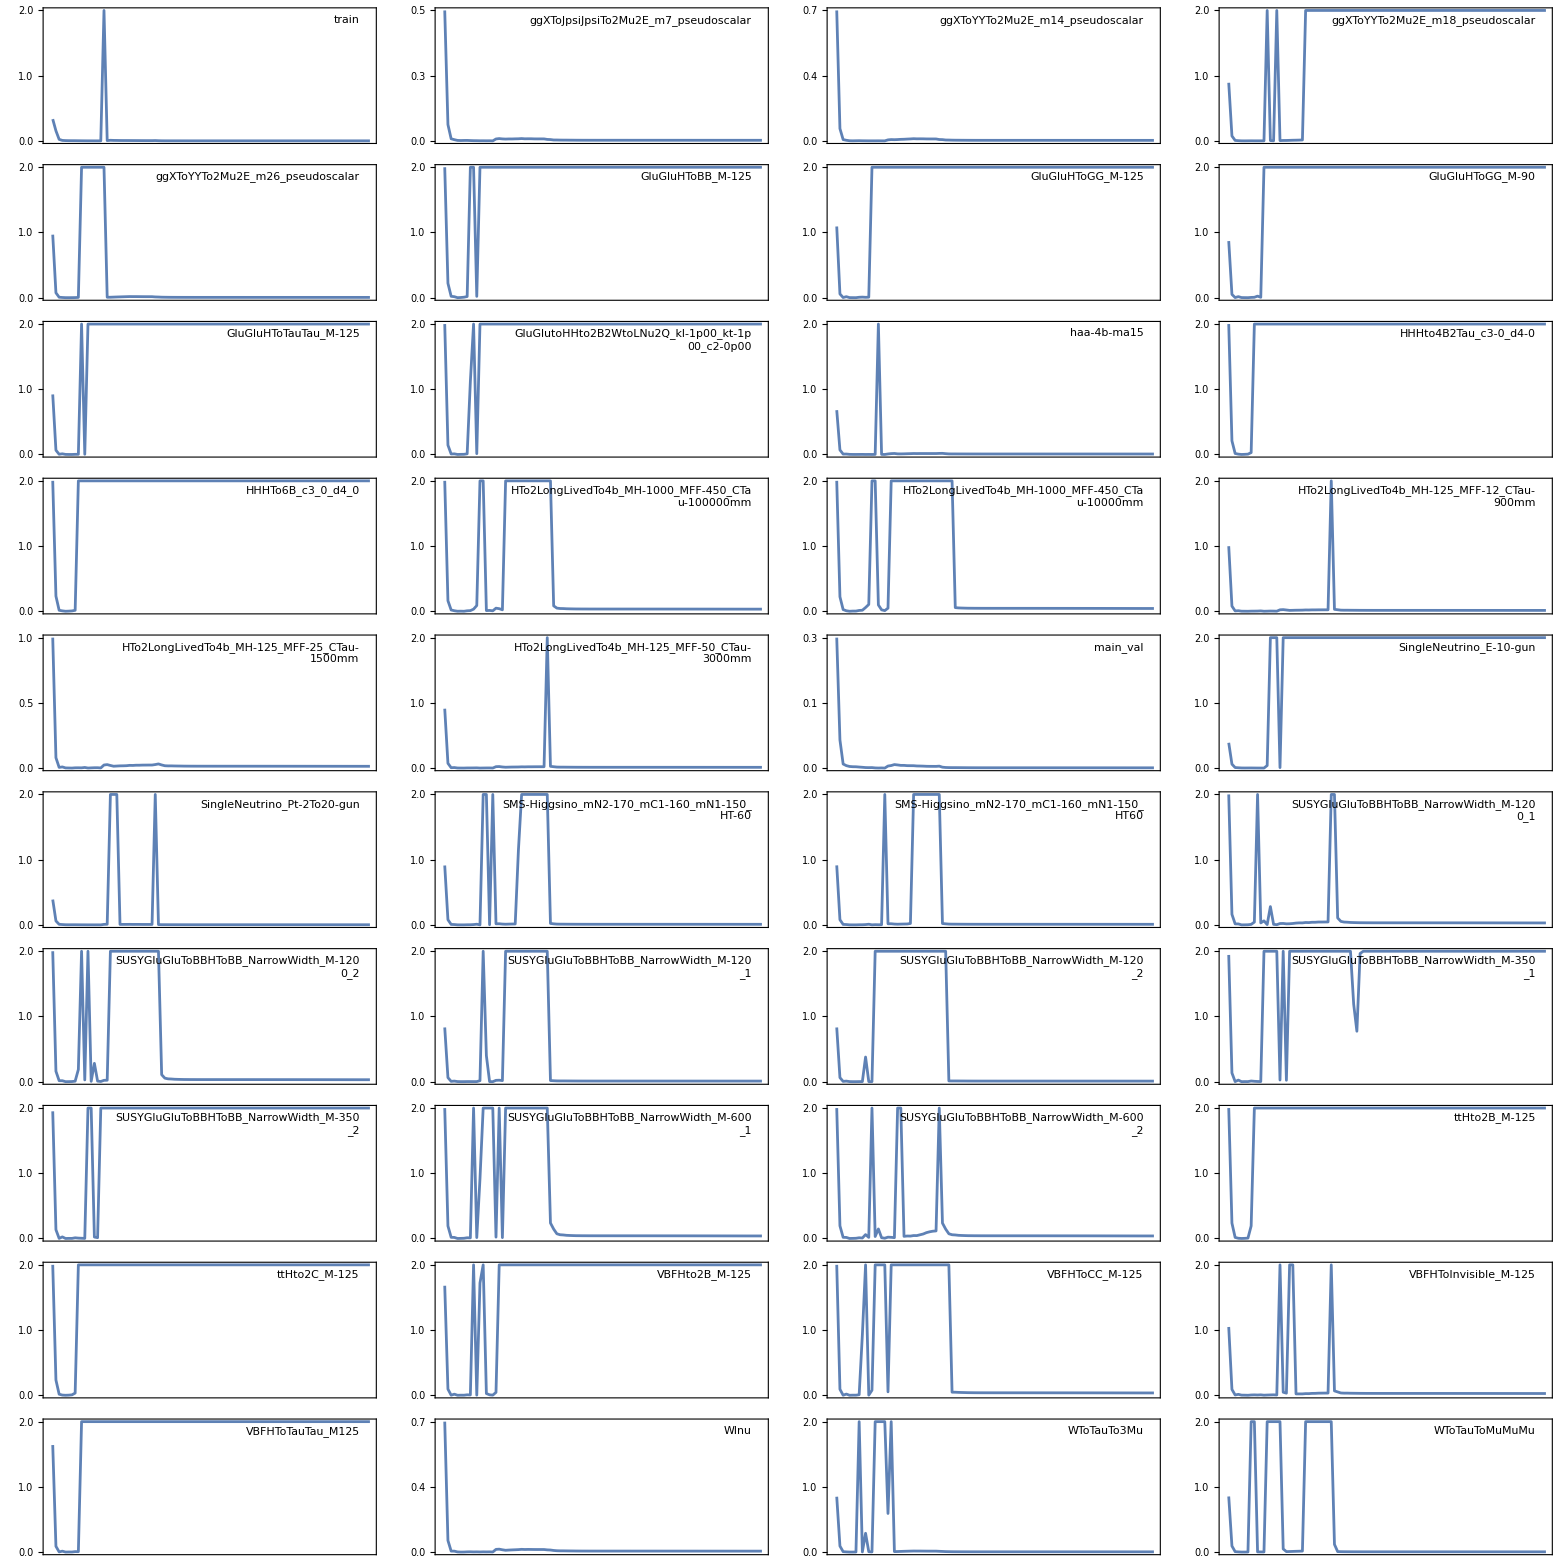
kl | -Graphics-
 | Epochs ∈ [0, 100]

```mathematica
makePlot[row_,label_]:=
ListLinePlot[
row,
PlotStyle->{Medium},
Axes->False,
Frame->True,
FrameTicks->{{{{Min[row],NumberForm[N[Min[row]],{5,1}]},{(Min[row]+(Max[row] - Min[row])/2),NumberForm[N[Min[row]+(Max[row] - Min[row])/2],{5,1}]},{Max[row],NumberForm[N[Max[row]],{5,1}]}},None},{None,None}},
FrameTicksStyle->Directive[11,FontWeight->"Plain"],
PlotRange->{All, {Min[row], Max[row]}},
ImageSize->300,PlotLabel->None,
Epilog->{Inset[Style[label,11,FontWeight->"Plain",Background->White],Scaled[{0.95,0.95}],{Right,Top}]}
];
plots=MapThread[makePlot,{Values[plotData],datasetNamesWrapped}];

possiblePartitions = Divisors[Length@datasetNames];
plotsPerRow = possiblePartitions[[4]];
grid=Partition[plots,4];

fullGridWithAxes=Grid[{{"",Grid[grid,Spacings->{1,1},Alignment->Center]},{"",Style["Epochs ∈ [0, 100]",FontWeight->"SemiBold",24, Gray]}},Spacings->{1,2}];
Row[{Style[Rotate[desiredMetric,90 Degree],FontWeight->"SemiBold",24, Gray],Spacer[10],fullGridWithAxes}]
```

```mathematica
Export["dataset_grids/" <>FileBaseName@desiredMetric <> "_" <>desiredRun <> ".png",%]
```

dataset_grids/loss_scan_lr0.001_alpha0.6.png

# Summary Plot

```mathematica
processRunName[runName_] := (
name = {};
splitRunName = StringSplit[runName,"_"];
lrName = Select[splitRunName, StringContainsQ["lr"]];
alphaName =Select[splitRunName, StringContainsQ["alpha"]];
name =Append[name, "ℓ = "<>Flatten@StringCases[lrName,NumberString] <> ", " <> "α = "<>Flatten@StringCases[alphaName,NumberString]];
name
)

datasetPlotStyling=<|
"train"->"ZeroBias_train",
"ggXToJpsiJpsiTo2Mu2E_m7_pseudoscalar"->"gg → X_(7 GeV) → J/ψ J/ψ → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m14_pseudoscalar"->"gg → X_(14 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m18_pseudoscalar"->"gg → X_(18 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m26_pseudoscalar"->"gg → X_(26 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"GluGluHToBB_M-125"-> "gg → H(125 GeV) → bb̄",
"GluGluHToGG_M-125"-> "gg → H(125 GeV) → gg",
"GluGluHToGG_M-90"->"gg → H(90 GeV) → gg", 
"GluGluHToTauTau_M-125"-> "gg → H(125 GeV) → τ^+τ^-",
"GluGlutoHHto2B2WtoLNu2Q_kl-1p00_kt-1p00_c2-0p00"-> "gg → HH → bb̄W^+W^- → (l^±ν)(qq̄')",
"HHHto4B2Tau_c3-0_d4-0" -> "HHH → bb̄bb̄τ^+τ^-",
"HHHTo6B_c3_0_d4_0"->"HHH → 6b",
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-100000mm"-> "H (10^3 GeV) → LL (10^3 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-12_CTau-900mm" -> "H (125 GeV) → LL (900 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-25_CTau-1500mm" ->"H (125 GeV) → LL (1500 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-50_CTau-3000mm" -> "H (125 GeV) → LL (3000 mm) → 4b",
"haa-4b-ma15"->"H → AA → 4b", 
"VBFHto2B_M-125"->"VV → H → bb̄", 
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-10000mm" -> "H (10^3 GeV) → 2LL (10^4 mm) → 4b", 
"main_val"->"ZeroBias",
"SingleNeutrino_E-10-gun" -> "Background Sim 1",
"SingleNeutrino_Pt-2To20-gun" -> "Background Sim 2",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT-60" -> "higgsino 1",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT60" ->"higgsino 2",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_1" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_2" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_1" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_2" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_1" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_2" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_1" -> "gg → bb̄H(600 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_2"-> "gg → bb̄H(600 GeV) → bb̄",
"ttHto2B_M-125" -> "tt̄ → H(125 GeV) → bb̄",
"ttHto2C_M-125" -> "tt̄ → H(125 GeV) → cc̄",
"VBFHToCC_M-125"->"VV → H → cc̄",
"VBFHToInvisible_M-125"->"VV → H → invis",
"VBFHToTauTau_M125"->"VV → H → τ^+τ^-",
"Wlnu" -> "W^± → l^±ν_l",
"WToTauTo3Mu" -> "W^± → τ^± → μ^±μ^+μ^-",
"WToTauToMuMuMu" -> "W^± → τ^± → μ^±μ^+μ^-"
|>;

(*Select which datasets to plot.*)
plottedDatasets = {"haa-4b-ma15", "GluGluHToGG_M-90","VBFHToTauTau_M125" };
data = KeyTake[plotData,plottedDatasets];
data = KeyValueMap[Function[{key,mat},key->Module[{nelements=Dimensions[mat][[1]]},Table[{i,mat[[i]]},{i, nelements}]]],data];

(*Color function for selected lines*)
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
colorFunc=Function[i,RGBColor[hexColors[[Mod[i-1,Length[hexColors]]+1]]]];

(*Extract and scale series*)
series=Values[data];

(*Determine scaling for y-values:two significant figures*)
allYRaw=Flatten[series[[All,All,2]]];
scaleExp=Floor[Log10[Max[Abs[allYRaw]]]];
scaleFactor=10^scaleExp;

scaledSeries=Map[{#[[1]],#[[2]]/scaleFactor}&,series,{2}];

(*Legend labels*)
labelsKeys=Style[#,FontSize->25, Italic]&/@(datasetPlotStyling/@plottedDatasets);

(*X-axis ticks:major every 5,minor every 1*)
numCols=Length@First@series;
majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
majorPositions=Range[1,numCols,5];
majorTicks=Table[{i,i-1,{majorLen,0}},{i,majorPositions}];
minorPositions=Complement[Range[1,numCols],majorPositions];
minorTicks=Table[{i,"",{minorLen,0}},{i,minorPositions}];
xTicks=Join[majorTicks,minorTicks];
xTicksUpper=xTicks/. {v_,_,len_}:>{v,"",len};

(*Y-axis ticks:5 intervals on scaled data,formatted to 2 significant figures*)
allY=Flatten[scaledSeries[[All,All,2]]];
yMin=Min[allY];
yMax=Max[allY];
yStep=(yMax-yMin)/5;
(*Major Y-ticks*)
majorPositionsY=Table[yMin+i*yStep,{i,0,5}];
majorTicksY=Table[{pos,NumberForm[pos,{3,2}],{majorLen,0}},{pos,majorPositionsY}];
(*Minor Y-ticks:5 between majors*)
minorTicksY=Flatten[Table[Table[{majorPositionsY[[k]]+j*(yStep/6),"",{minorLen,0}},{j,1,5}],{k,1,Length[majorPositionsY]-1}],1];
(*Combined Y-ticks*)
yTicks=Join[majorTicksY,minorTicksY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};

legendY=0.8;          (*how low the legend sits (0=bottom,1=top)*)
ruleY=legendY+0.11;(*y of the horizontal line,tweak as needed*)

legendPosition = {Scaled[{0.9,legendY}], Scaled[{0.991,0.99}],Scaled[{0.765,ruleY}], Scaled[{1.031,ruleY}]};
shift={-0.08,-0.2};  
legendPosition=legendPosition/. Scaled[p_]:>Scaled[p+shift];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
leftPad=150;   (*room for y ticks+your CMS tag*)
topPad=70;    (*room above frame*)

tevText = Row[{Style["14 TeV",FontFamily->"TeX Gyre Heros",24],""}];
(*Plot*)
plt =ListLinePlot[
scaledSeries,
Joined->True,
Axes->False,
Frame->True,
PlotRange->All,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksUpper}},FrameLabel->{Style["Epoch",Black,FontSize->30,FontFamily->"TeX Gyre Heros"],Style[Row[{desiredMetricPlotStyling[desiredMetric],If[scaleExp!=0," ×",""],If[scaleExp!=0,Superscript[10,scaleExp]], ""}],Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},PlotStyle->(colorFunc/@Range[Length@series]),
PlotLegends->Placed[SwatchLegend[labelsKeys,LegendMarkerSize->18,LabelStyle->Directive[Black,FontSize->18,FontFamily->"TeX Gyre Heros"]],legendPosition[[1]]],
LabelStyle->Directive[Black,FontSize->28,FontFamily->"TeX Gyre Heros"],
FrameTicksStyle->Directive[AbsoluteThickness[2]],
Epilog->{
Text[Row[{Style[processRunName[desiredRun][[1]],FontFamily->"TeX Gyre Heros",FontSize->28]}],legendPosition[[2]],{Right,Top}],
{GrayLevel[.2],AbsoluteThickness[3],Line[{legendPosition[[3]],legendPosition[[4]]}]} ,
},
PlotRangePadding->{{Scaled[0.01],Scaled[0.017]},{Scaled[0.04],Scaled[0.04]}},
ImageSize->1300,
AspectRatio->0.5
];
outer=Graphics[{Inset[plt,Scaled[{0,0}],{Left,Bottom},Scaled[1]],Inset[cmsText,Scaled[{0.08,0.93}],{Left,Bottom},Scaled[1]] (*top-left outside*), Inset[tevText,Scaled[{0.815,0.94}],{Left,Bottom},Scaled[1]]},PlotRange->{{0,1},{0,1}}, AspectRatio->0.5, ImageSize->1300]
```

-Graphics-

```mathematica
Export["final_presentation_plots/" <>"3signal_" <> desiredMetric <>"_" <> desiredRun <>".pdf",outer]
```

final_presentation_plots/3signal_kl_scan_lr0.001_alpha0.6.pdf